```mathematica
SetDirectory[NotebookDirectory[]];
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
nb[mb2_,q_,T_]:=1/(Exp[(√(q^2+mb2))/T]-1);
nbd1x[mb2_,q_,T_]:=-1/T nb[mb2,q,T](nb[mb2,q,T]+1);
mf2[h_,ρ_]:=(h^2 ρ)/2;
Eq[q_,mf2_]:=√(q^2+mf2);
Epi[q_,mp2_]:=√(q^2+mp2);
Nf=2;
Nc=3;
h=6.5;
λ=20.;
ν=-490.^2;
c=1.7*10^-3*(10^3)^3;
μ=0.;
M1=700;
F1B1thr[mp2_,mf2_,p0_,q_,T_,mu_]:=1/2 (-nb[mp2,q,T]/(Epi[q,mp2] (-Eq[q,mf2]^2+(Epi[q,mp2]- mu+ⅈ p0)^2))-(nb[mp2,q,T]+1)/(Epi[q,mp2] (-Eq[q,mf2]^2+(-Epi[q,mp2]-mu+ⅈ p0)^2))+nfa[mf2,q,T,mu]/(Eq[q,mf2] (-Epi[q,mp2]^2+(-Eq[q,mf2]-mu+ⅈ p0)^2))+(-1+nff[mf2,q,T,mu])/(Eq[q,mf2] (-Epi[q,mp2]^2+(Eq[q,mf2]-mu+ⅈ p0)^2)));
F2B1thr[mp2_,mf2_,p0_,q_,T_,mu_]:=1/2 (nb[mp2,q,T]/(Epi[q,mp2] ((-0mu+ⅈ p0+Epi[q,mp2])^2-Eq[q,mf2]^2)^2)+(1+nb[mp2,q,T])/(Epi[q,mp2] ((-0mu+ⅈ p0-Epi[q,mp2])^2-Eq[q,mf2]^2)^2)+nfa[mf2,q,T,mu]/(2 (-Epi[q,mp2]^2+(-0mu+ⅈ p0-Eq[q,mf2])^2) Eq[q,mf2]^3)-((-0mu+ⅈ p0-Eq[q,mf2]) nfa[mf2,q,T,mu])/((-Epi[q,mp2]^2+(-0mu+ⅈ p0-Eq[q,mf2])^2)^2 Eq[q,mf2]^2)-nfd1xa[mf2,q,T,mu]/(2 (-Epi[q,mp2]^2+(-0mu+ⅈ p0-Eq[q,mf2])^2) Eq[q,mf2]^2)-nfd1xf[mf2,q,T,mu]/(2 Eq[q,mf2]^2 (-Epi[q,mp2]^2+(-0mu+ⅈ p0+Eq[q,mf2])^2))+((-0mu+ⅈ p0+Eq[q,mf2]) (-1+nff[mf2,q,T,mu]))/(Eq[q,mf2]^2 (-Epi[q,mp2]^2+(-0mu+ⅈ p0+Eq[q,mf2])^2)^2)+(-1+nff[mf2,q,T,mu])/(2 Eq[q,mf2]^3 (-Epi[q,mp2]^2+(-0mu+ⅈ p0+Eq[q,mf2])^2)));
hT[mp2_,ms2_,mf2_,h_,p0_,T_,mu_]:=1/(2Nf)*h^3/(2 π^2)NIntegrate[q^2 Re[-F1B1thr[ms2,mf2,p0,q,T,mu]+ 2mf2 F2B1thr[ms2,mf2,p0,q,T,mu]],{q,0,10,20,30,40,50,100,200,300,1000,5000},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0,Method->{"GaussBerntsenEspelidRule","Points"->20}},MaxRecursion->20]-(Nf^2-1)/(2Nf)*h^3/(2 π^2)NIntegrate[q^2 Re[-F1B1thr[mp2,mf2,p0,q,T,mu]+ 2mf2 F2B1thr[mp2,mf2,p0,q,T,mu]],{q,0,10,20,30,40,50,100,200,300,1000,5000},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0,Method->{"GaussBerntsenEspelidRule","Points"->20}},MaxRecursion->20]
hpiT[mp2_,ms2_,mf2_,h_,p0_,T_,mu_]:=1/(2Nf)*h^3/(2 π^2)NIntegrate[q^2 Re[F1B1thr[ms2,mf2,p0,q,T,mu]],{q,0,10,20,30,40,50,100,200,300,1000,5000},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0,Method->{"GaussBerntsenEspelidRule","Points"->20}},MaxRecursion->20]-(Nf^2-1)/(2Nf)*h^3/(2 π^2)NIntegrate[q^2 Re[F1B1thr[mp2,mf2,p0,q,T,mu]],{q,0,10,20,30,40,50,100,200,300,1000,5000},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0,Method->{"GaussBerntsenEspelidRule","Points"->20}},MaxRecursion->20]
```

```mathematica
CloseKernels[];
LaunchKernels[18];
$KernelCount
```

18

```mathematica
fpidata=Flatten[Import["./sigma_T_mu0.dat"]];
mpdata=Flatten[Import["./mpion_T_mu0.dat"]];
msdata=Flatten[Import["./msigma_T_mu0.dat"]];
```

```mathematica
(*data=Table[hT[mpdata[[1]]^2,msdata[[1]]^2,mf2[6.5,fpidata[[T]]^2/2],6.5,π T,T,0],{T,1,300}];*)
data2=Table[{i*10,(-hpiT[mpdata[[i]]^2,msdata[[i]]^2,mf2[6.5,fpidata[[i]]^2/2],6.5,π i*10,i*10,0])^1},{i,1,200}];
```

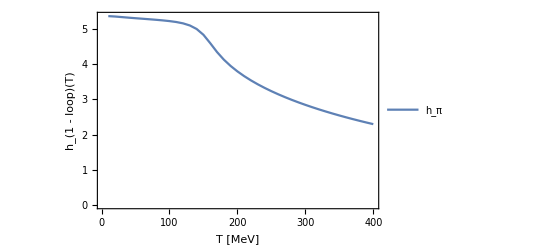

```mathematica
ListLinePlot[data2[[1;;40]],PlotRange->All,Frame->True,FrameLabel->{"T [MeV]","h_(1 - loop)(T)"},PlotLegends->{(*"h_σ",*)"h_π"},ScalingFunctions->{Automatic,Automatic}]
```

## Zpi phase

```mathematica
sigma0=Import["../sigma0.dat"];
sigma0p2=Import["../sigma0p2.dat"];
mu=Table[i*5.,{i,1,80}];
mu2=Table[i,{i,290,310}];
T=Table[i,{i,1,300}];
mpdata=Import["../mpion_T_mu.dat"];
msdata=Import["../msigma_T_mu.dat"];
mpdata2=Import["../mpion_T_mu_p2.dat"];
msdata2=Import["../msigma_T_mu_p2.dat"];
```

```mathematica
hdata1=ParallelTable[Table[-hpiT[(mpdata[[j]][[T]])^2,(msdata[[j]][[T]])^2,mf2[6.5,(sigma0[[j]][[T]])^2/2],6.5,π T,T,mu[[j]]]+hpiT[(mpdata[[1]][[1]])^2,(msdata[[1]][[1]])^2,mf2[6.5,(sigma0[[1]][[1]])^2/2],6.5,π 1,1,mu[[1]]]+6.5//Quiet,{T,1,300}],{j,1,80}];
hdata2=ParallelTable[Table[-hpiT[(mpdata2[[j]][[T]])^2,(msdata2[[j]][[T]])^2,mf2[6.5,(sigma0p2[[j]][[T]])^2/2],6.5,π T,T,mu2[[j]]]+hpiT[(mpdata[[1]][[1]])^2,(msdata[[1]][[1]])^2,mf2[6.5,(sigma0[[1]][[1]])^2/2],6.5,π 1,1,mu[[1]]]+6.5//Quiet,{T,1,300}],{j,1,21}];
```

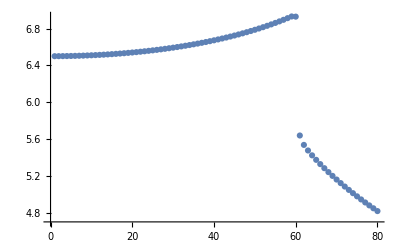

```mathematica
ListPlot[{Transpose[hdata1][[1]]}]
```

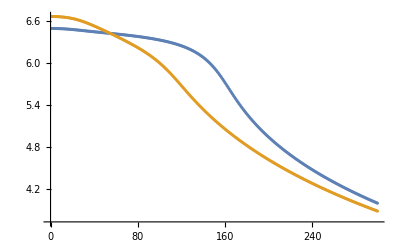

```mathematica
ListPlot[{hdata1[[1]],hdata1[[40]]},PlotRange->All]
```

```mathematica
Export["./hdata1.dat",hdata1];
Export["./hdata2.dat",hdata2];
```

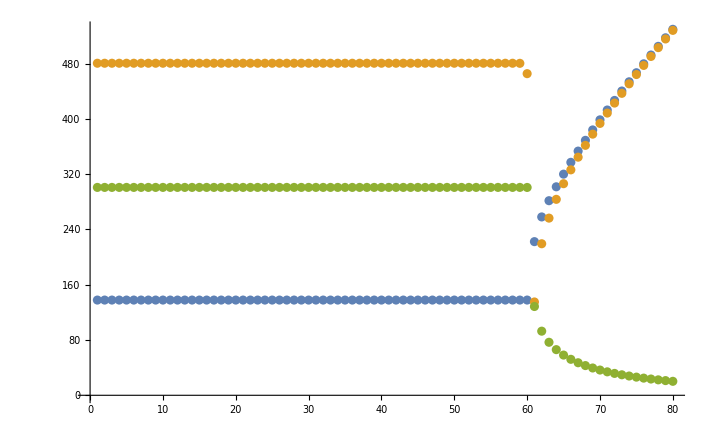

```mathematica
ListPlot[{Transpose[mpdata][[1]],Transpose[msdata][[1]],(√(6.5^2*Transpose[sigma0][[1]]^2))/2}]
```